```mathematica
U = Import["C:\\Users\\sammy\\OneDrive\\Documents\\FEM_DISSERTATION\\DISSERTATION\\FEM_Project\\1DExample.dat"]
```

{{0.,0.},{0.25,0.5},{0.5,1.},{0.75,0.5},{1.,0.}}

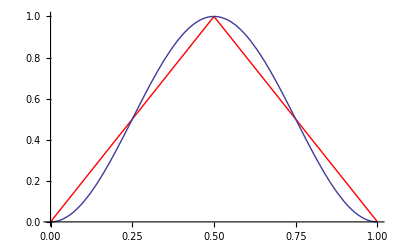

```mathematica
lp =ListPlot[U,Joined->True, PlotStyle->{Red}];
plot = Plot[Sin[Pi*x]^2,{x,0,1}];
Show[lp,plot]
```